```mathematica
(*aTimp1FN=FileNames["/Users/Avimayo/Desktop/aTIMP1/dblre- analysis IgG_aTIMP1_FULLslides_270524/export/*s.xlsx"]*)
```

```mathematica
(*aTimp1=Import[#][[1]]&/@FileNames["/Users/Avimayo/Desktop/aTIMP1/dblre- analysis IgG_aTIMP1_FULLslides_270524/export/*s.xlsx"];*)
```

```mathematica
(*SortedData=(SortBy[GatherBy[#,#[[3]]&],#[[1,3]]&]&/@FindClusters[#[[;;2]]->#&/@#[[2;;,{8,9,5}]],Method->"DBSCAN"])&/@(DeleteCases[#,{_,""..}]&/@aTimp1);*)
```

```mathematica
SortedData=Uncompress@;
```

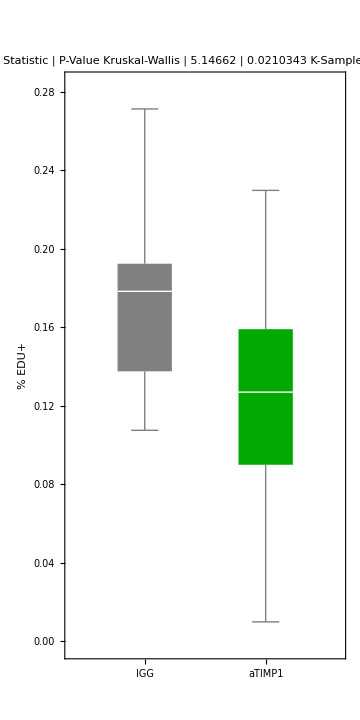
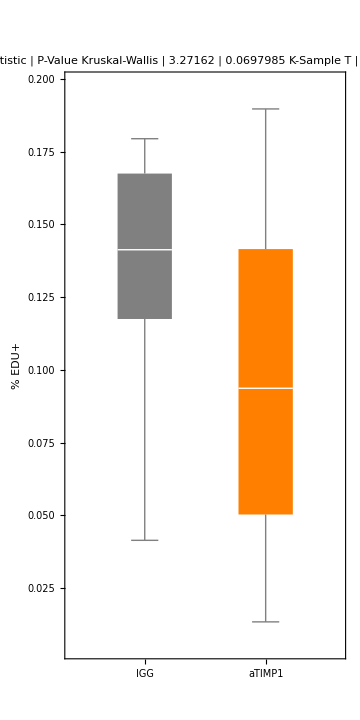
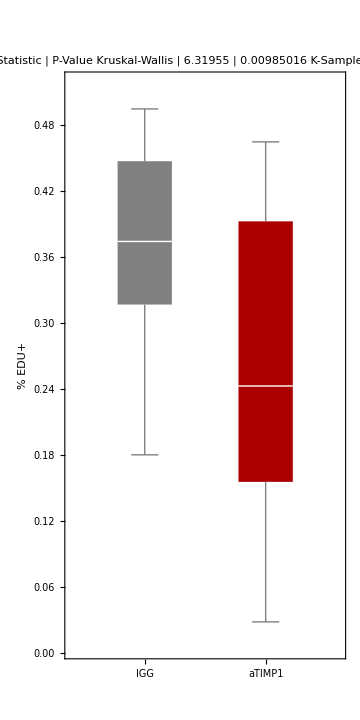

```mathematica
Row[Table[BoxWhiskerChart[#,PlotLabel->TableForm@{{"Macrophages","Other","MyoFibroblasts"}[[p]],LocationEquivalenceTest[#,{"TestDataTable",All}]},ChartStyle->{Gray,{Darker@Green,Orange,Darker@Red}[[p]]},ChartLabels->{"IGG","aTIMP1"},AspectRatio->2,FrameLabel->{Automatic,"% EDU+"},ImageSize->Medium]&@(Flatten/@TakeList[#,{4,5}]&@Map[N@((#[[2]])/(Total@#))&@(Length/@#)&,SortedData[[{8,5,3,1,2,4,6,7,9},;;,{{1,2},{3,4},{5,6}}[[p]]]],{2}]),{p,{1,2,3}}],Spacer@10]
```

```mathematica
TableForm[{
TakeList[SortBy[#,First]&/@Map[(Length/@#)&,SortedData[[{8,5,3,1,2,4,6,7,9},;;,{{1,2},{3,4},{5,6}}[[1]]]],{2}],{4,5}],
TakeList[SortBy[#,First]&/@Map[(Length/@#)&,SortedData[[{8,5,3,1,2,4,6,7,9},;;,{{1,2},{3,4},{5,6}}[[2]]]],{2}],{4,5}],
TakeList[SortBy[#,First]&/@Map[(Length/@#)&,SortedData[[{8,5,3,1,2,4,6,7,9},;;,{{1,2},{3,4},{5,6}}[[3]]]],{2}],{4,5}]},
TableHeadings->{{"M","Other","myoF"},{"IgG","aTimp1"}},TableAlignments->{Center, Center},TableDepth->4]
```

| IgG | aTimp1
M | {355,53} | {497,185} |  |  | 
{1282,277} | {1342,228} | {2034,245} | {2722,337} | {3103,691}
{1587,414} | {1990,475} | {2082,495} | {2399,669} | {2965,545}
{1401,238} | {1546,337} | {2098,307} | {2109,483} |  | {147,42} | {191,34} | {715,17} | {1546,206} | {2811,686} | {2873,857}
{1027,105} | {1469,220} | {1819,204} | {1949,173} |  | 
{168,10} | {500,5} | {1339,101} | {3210,718} |  | 
{727,97} | {1671,278} | {2173,316} |  |  | 
{104,15} | {376,60} | {799,127} | {2069,483} |  | 
Other | {4124,902} | {12724,1725} |  |  | 
{17388,2447} | {17418,3745} | {23393,3820} | {24869,1287} | {29343,1266}
{10003,2086} | {13735,2748} | {14044,2664} | {15336,3102} | {27357,4775}
{14056,2330} | {18651,3040} | {20499,2572} | {24360,3183} |  | {4001,255} | {4057,214} | {9450,2020} | {9548,1567} | {10938,197} | {13120,1980}
{8410,869} | {8538,443} | {9235,1280} | {16154,1623} |  | 
{3636,190} | {7184,97} | {11134,749} | {16015,3253} |  | 
{9070,1172} | {9990,529} | {10814,1806} |  |  | 
{12136,2651} | {12537,1478} | {13637,1262} | {15304,3583} |  | 
myoF | {567,351} | {1212,1085} |  |  | 
{1154,623} | {1538,882} | {1830,1035} | {1859,408} | {1959,433}
{1514,1383} | {1705,1333} | {1772,1736} | {2113,1703} | {2244,1823}
{1676,1123} | {2043,1180} | {2417,954} | {2750,1014} |  | {298,204} | {309,98} | {1666,88} | {2322,829} | {2740,2198} | {3297,2752}
{1888,326} | {2271,694} | {2607,881} | {3196,600} |  | 
{326,43} | {1082,110} | {1324,38} | {1569,1108} |  | 
{1527,401} | {2585,951} | {3333,1448} |  |  | 
{884,768} | {1147,296} | {2007,643} | {2867,1817} |  |

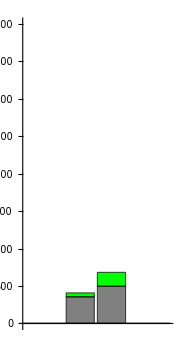
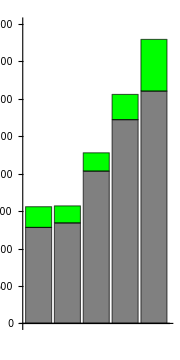
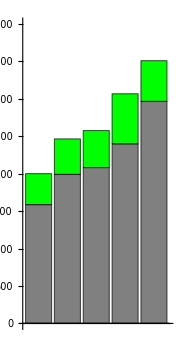
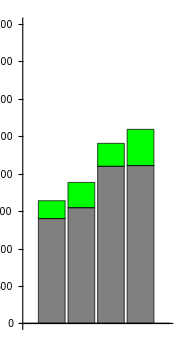
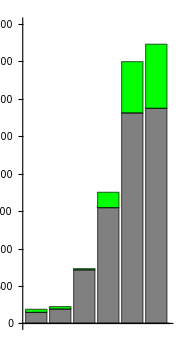
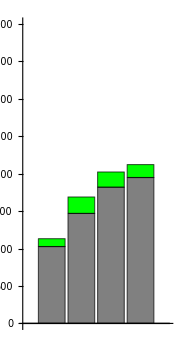
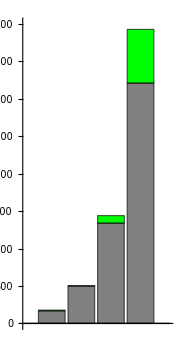
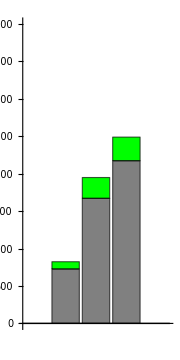
| IgG | aTimp1
M | -Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics--Graphics-
myoF | -Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
TableForm[{
Row[#,Spacer@10,Frame->True]&/@Map[
BarChart[#,ChartLayout->"Stacked",AspectRatio->2,PlotRange->{0,4000},ChartStyle->{Gray,Green},ImageSize->Small]&,TakeList[SortBy[#,First]&/@Map[(Length/@#)&,SortedData[[{8,5,3,1,2,4,6,7,9},;;,{{1,2},{3,4},{5,6}}[[1]]]],{2}],{4,5}],
{2}],
Row[#,Spacer@10,Frame->True]&/@Map[
BarChart[#,ChartLayout->"Stacked",AspectRatio->2,PlotRange->{0,6000},ChartStyle->{Gray,Red},ImageSize->Small]&,TakeList[SortBy[#,First]&/@Map[(Length/@#)&,SortedData[[{8,5,3,1,2,4,6,7,9},;;,{{1,2},{3,4},{5,6}}[[3]]]],{2}],{4,5}],
{2}]},TableHeadings->{{"M","myoF"},{"IgG","aTimp1"}},TableAlignments->{Center, Center}]
```

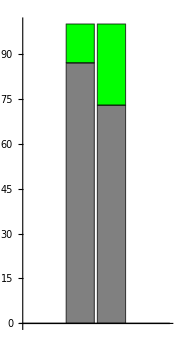
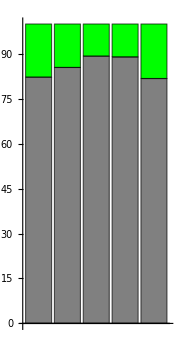
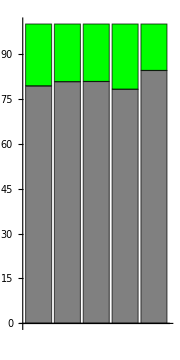
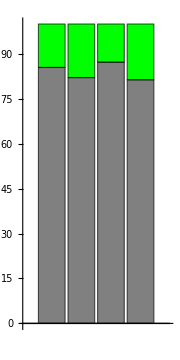
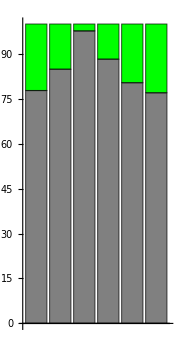
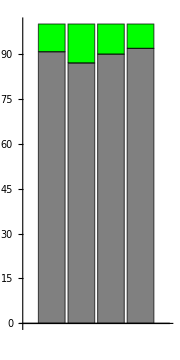
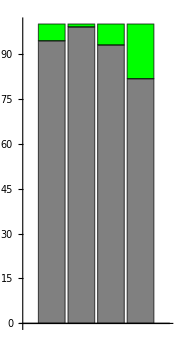
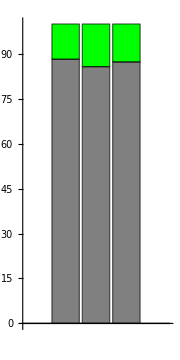
| IgG | aTimp1
M | -Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics--Graphics-
myoF | -Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
TableForm[{
Row[#,Spacer@10,Frame->True]&/@Map[
BarChart[#,ChartLayout->"Percentile",AspectRatio->2,PlotRange->{0,100},ChartStyle->{Gray,Green},ImageSize->Small]&,TakeList[SortBy[#,First]&/@Map[(Length/@#)&,SortedData[[{8,5,3,1,2,4,6,7,9},;;,{{1,2},{3,4},{5,6}}[[1]]]],{2}],{4,5}],
{2}],
Row[#,Spacer@10,Frame->True]&/@Map[
BarChart[#,ChartLayout->"Percentile",AspectRatio->2,PlotRange->{0,100},ChartStyle->{Gray,Red},ImageSize->Small]&,TakeList[SortBy[#,First]&/@Map[(Length/@#)&,SortedData[[{8,5,3,1,2,4,6,7,9},;;,{{1,2},{3,4},{5,6}}[[3]]]],{2}],{4,5}],
{2}]},TableHeadings->{{"M","myoF"},{"IgG","aTimp1"}},TableAlignments->{Center, Center}]
```

```mathematica
TableForm[Table[Total/@Flatten/@TakeList[#,{4,5}]&@Map[N@((#[[2]])/(1(*Total@#*)))&@(Length/@#)&,SortedData[[{8,5,3,1,2,4,6,7,9},;;,{{1,2},{3,4},{5,6}}[[p]]]],{2}],{p,{1,3}}],TableHeadings->{{"M","myoF"},{"IgG","aTimp1"}}]
```

| IgG | aTimp1
M | 5979. | 4754.
myoF | 17066. | 16293.

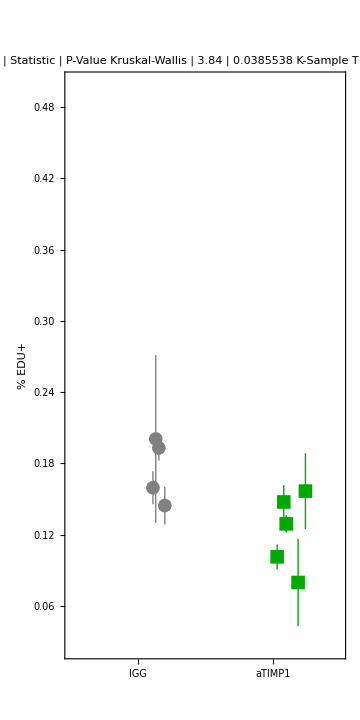
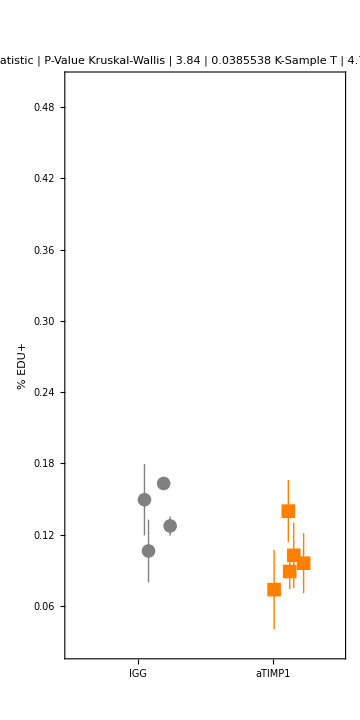
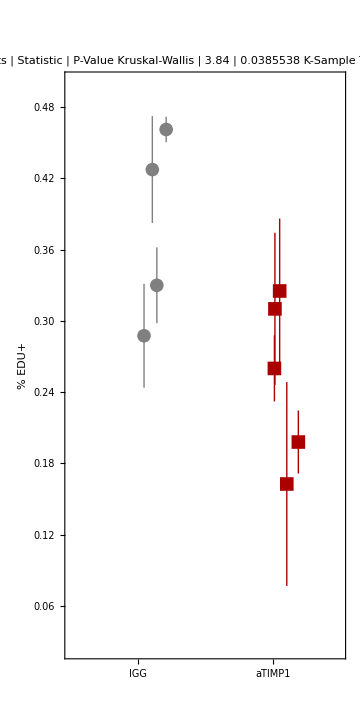

```mathematica
Row[
Table[
ListPlot[#,PlotMarkers->{Automatic,14},AspectRatio->2,PlotLabel->TableForm@{{{"Macrophages","Other","MyoFibroblasts"}[[p]]},LocationEquivalenceTest[#[[;;,;;,2,1]],{"TestDataTable",All}]},FrameLabel->{Automatic,"% EDU+"},ImageSize->Medium,Frame->True,PlotRangePadding->None,Axes->False,FrameTicks->{{Automatic,None},{{{1,2},{"IGG","aTIMP1"}}ᵀ,None}},PlotRange->{{0.5,2.5},{0.025,.5}},PlotStyle->{Gray,{Darker@Green,Orange,Darker@Red}[[p]]}]&@MapIndexed[
Thread[{#2[[1]],#}]/.x_Integer:>x+.25RandomReal[]&,
TakeList[
MeanAround/@Map[N@((#[[2]])/(Total@#))&@(Length/@#)&,SortedData[[{8,5,3,1,2,4,6,7,9},;;,{{1,2},{3,4},{5,6}}[[p]]]],{2}],
{4,5}]],
{p,{1,2,3}}],Spacer@10]
```

```mathematica
allsection=Join@@@((Join@@SortedData[[{8,5,3,1,2,4,6,7,9}]]));
```

```mathematica
allsectionshifted=GatherBy[SortBy[Thread[{(#[[;;,;;2]]-Threaded[Min/@(#[[;;,;;2]]ᵀ)]),#[[;;,3]]}],Last],Last][[;;,;;,1]]&/@allsection;
```

```mathematica
Coor2Array=ParallelMap[ArrayPad[SparseArray[Thread[(#-Min@#+1&/@(Round[#[[;;,;;2]]]ᵀ))ᵀ->#[[;;,3]]]&@#],50]&,Join@@Map[Join@@#&,SortedData[[{8,5,3,1,2,4,6,7,9}]],{2}]];
```

```mathematica
counts=ParallelTable[Sort[{#[[1,1]],#[[;;,2]]}&/@GatherBy[{#[[2]],Table[Count[#,c],{c,{"GFP: EdU-","GFP: EdU+","Other: EdU-","Other: EdU+","TdTom: EdU-","TdTom: EdU+"}}]&@DeleteCases[Extract[Threaded@#[[1]]+mask][d],0]}&/@Most@ArrayRules[d],First]],
{d,Coor2Array}];
```

```mathematica
Quiet@Map[Dimensions,fractions=TakeList[TakeList[Join@@@counts[[;;,;;,2]],{2,5,5,4,6,4,4,3,4}],{4,5}]/.x:{{_Integer..}..}:>(N@((#[[2;;;;2]])/(Total/@Partition[#,2]))&/@x),{3}]
```

{{{{8005,3},{15775,3}},{{36060,3},{23182,3},{30702,3},{33872,3},{25142,3}},{{39458,3},{21606,3},{18665,3},{24053,3},{23015,3}},{{33712,3},{27506,3},{21068,3},{28081,3}}},{{{16018,3},{13621,3},{24879,3},{4903,3},{19905,3},{4947,3}},{{15692,3},{21874,3},{15098,3},{13317,3}},{{25873,3},{14515,3},{9148,3},{4373,3}},{{19350,3},{13271,3},{16267,3}},{{17591,3},{22023,3},{16461,3},{20975,3}}}}

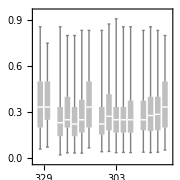
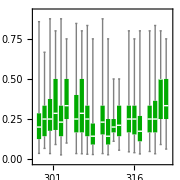
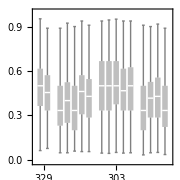
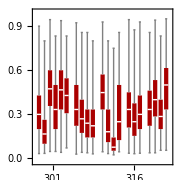
| Igg | aTimp1
Macro | -Graphics- | -Graphics-
MyoFib | -Graphics- | -Graphics-

```mathematica
TableForm[
Table[
MapIndexed[
BoxWhiskerChart[#,BarSpacing->{Small,Large},ImageSize->Small,AspectRatio->1,ChartStyle->{GrayLevel[.75],{Darker@Green,Black,Darker@Red}[[i]]}[[#2[[1]]]],
ChartLabels->{{{"329","314","303","300"},{"301","308","315","316","330"}}[[#2[[1]]]],None},FrameLabel->{None,"% EDU+"}]&,
DeleteCases[fractions[[;;,;;,;;,;;,i]],Indeterminate|0.|1.,∞]
],
{i,{1,3}}],TableHeadings->{{"Macro","MyoFib"},{"Igg","aTimp1"}},TableAlignments->{Center, Center}]
```

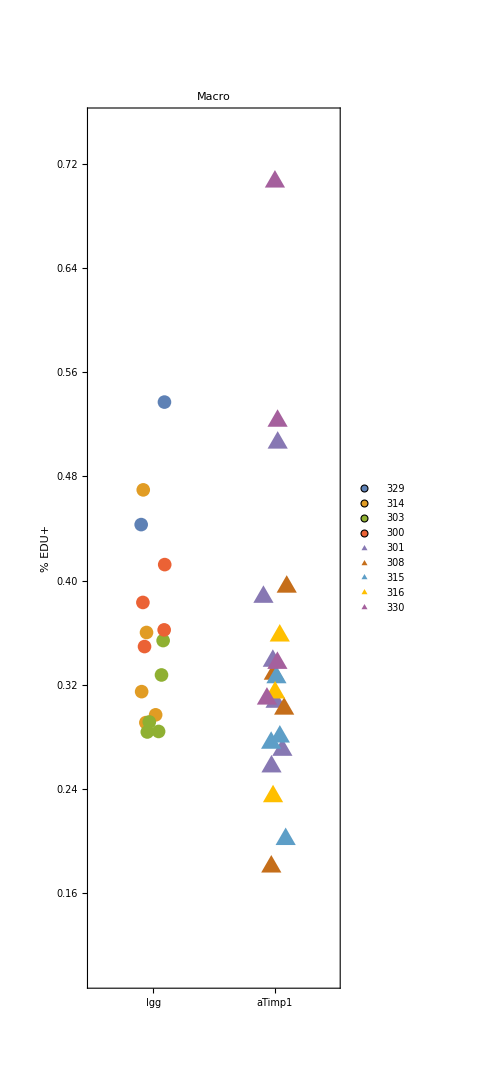
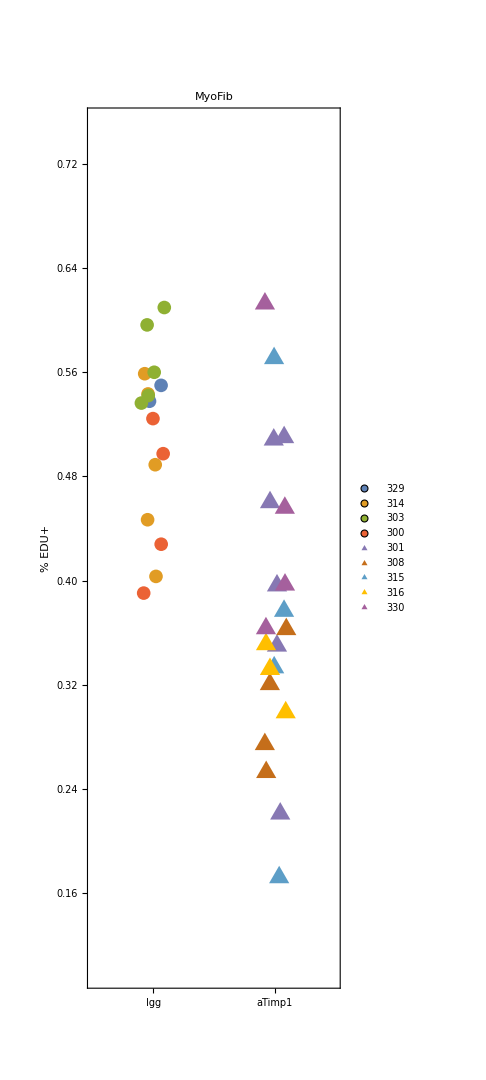

```mathematica
Row[
Table[
ListPlot[
Join@@Map[Thread,Thread/@({{1,2},Map[Mean@#&,DeleteCases[fractions[[;;,;;,;;,;;,i]],Indeterminate|0.,∞],{3}]}ᵀ),{2}]/.(x_Integer:>x+RandomReal[{-.1,.1}]),
AspectRatio->3,Frame->True,FrameTicks->{{Automatic,None},{{{1,"Igg"},{2,"aTimp1"}},None}},FrameLabel->{None,"% EDU+"},PlotRange->{{.5,2.5},{0.1,.75}},ImageSize->Medium,PlotStyle->PointSize[.05],PlotLegends->{"329","314","303","300","301","308","315","316","330"},PlotLabel->{"Macro","Other","MyoFib"}[[i]],PlotMarkers->Join[ConstantArray[{Graphics@Disk[],14},4],ConstantArray[{"▲",24},5]]],
{i,{1,3}}],
Spacer@20]
```

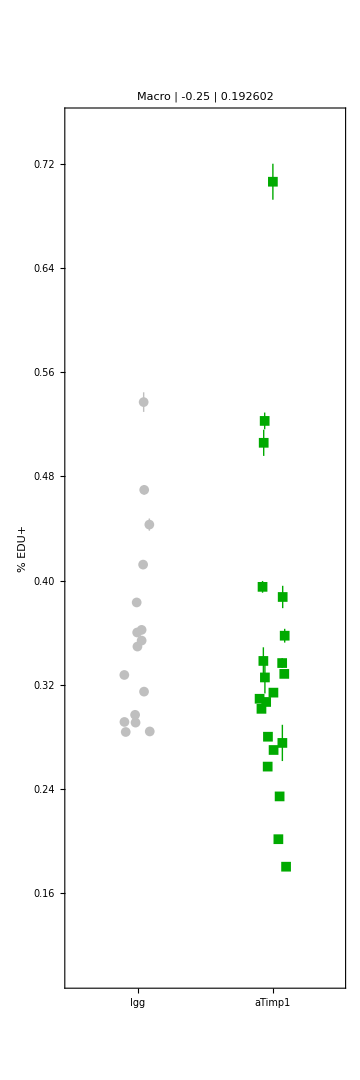
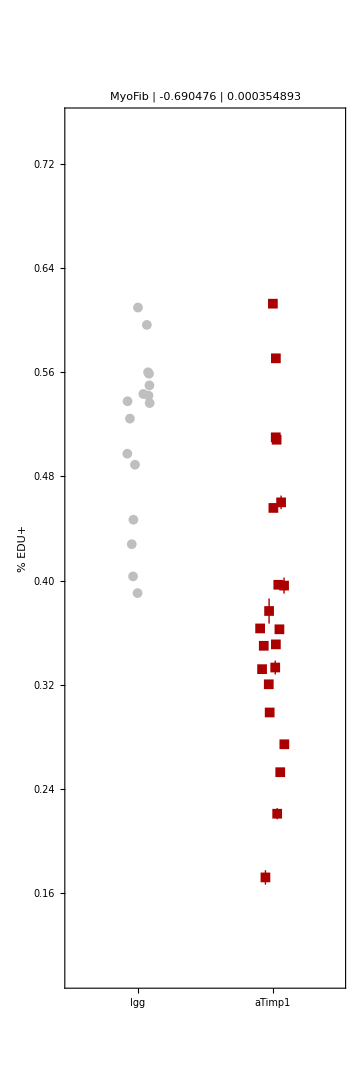

```mathematica
Row[
Table[
ListPlot[#,
PlotStyle->{GrayLevel[.75],{Darker@Green,Black,Darker@Red}[[i]]},AspectRatio->3,Frame->True,FrameTicks->{{Automatic,None},{{{1,"Igg"},{2,"aTimp1"}},None}},PlotRange->{{.5,2.5},{0.1,.75}},PlotMarkers->{Automatic,10},FrameLabel->{None,"% EDU+"},ImageSize->Medium,PlotLabel->TableForm[{{"Macro","Other","MyoFib"}[[i]],{1,0}+MannWhitneyTest[#[[;;,;;,2,1]],Automatic,"TestData"]/{-1/2 Times@@(Length/@#),1}},TableAlignments->Center]]&@(Thread/@({{1,2},Join@@@Map[Around[Mean@#,(StandardDeviation@#)/(√(Length@#))]&,DeleteCases[fractions[[;;,;;,;;,;;,i]],Indeterminate|0.,∞],{3}]}ᵀ)/.(x_Integer:>x+RandomReal[{-.1,.1}])),
{i,{1,3}}],Spacer@10]
```

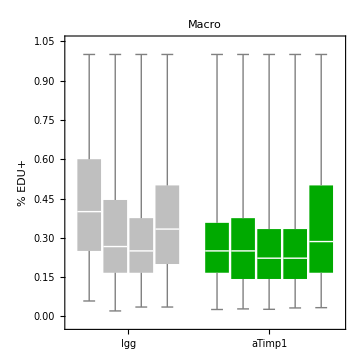
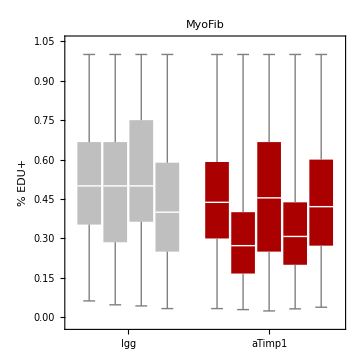

```mathematica
Row[Table[BoxWhiskerChart[#,BarSpacing->{Tiny,Large},FrameLabel->{None,"% EDU+"},ImageSize->Medium,AspectRatio->1,ChartStyle->{{GrayLevel[.75],{Darker@Green,Black,Darker@Red}[[i]]},None},ChartLabels->{{"Igg","aTimp1"},None},PlotLabel->{"Macro","Other","MyoFib"}[[i]]]&@DeleteCases[Map[Join@@#&,fractions[[;;,;;,;;,;;,i]],{2}],Indeterminate|0.,∞],{i,{1,3}}],Spacer@10]
```

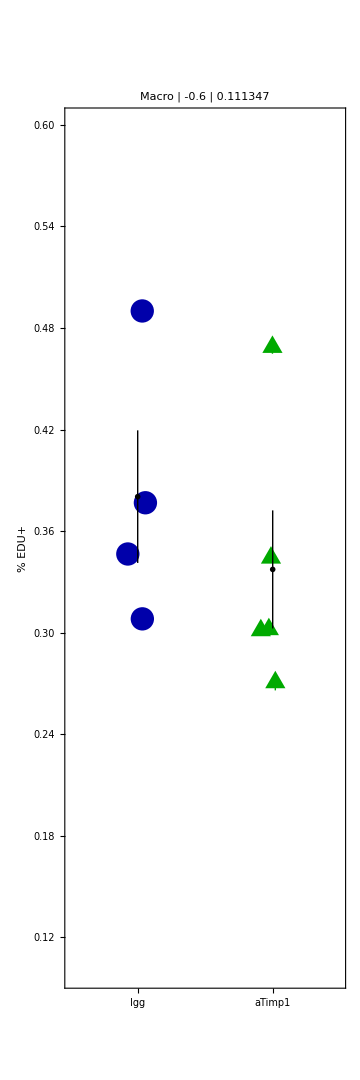
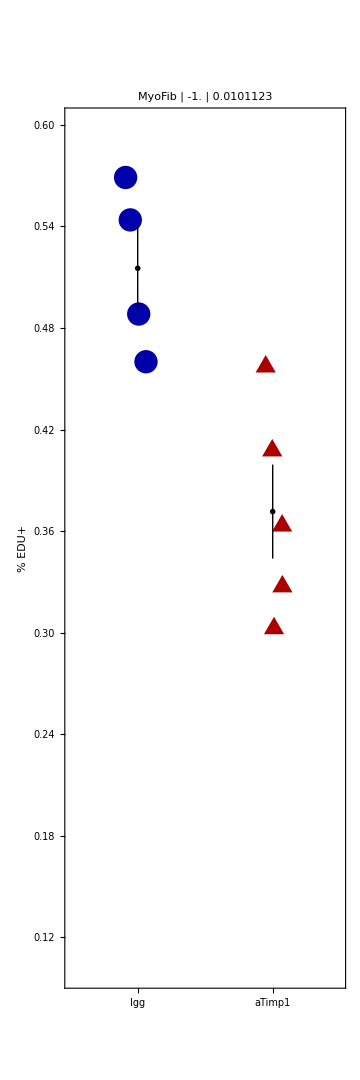

```mathematica
Row[Table[
Show[{
ListPlot[#,
PlotStyle->{Darker@Blue,{Darker@Green,Black,Darker@Red}[[i]]},AspectRatio->3,Frame->True,FrameTicks->{{Automatic,None},{{{1,"Igg"},{2,"aTimp1"}},None}},PlotRange->{{.5,2.5},{0.1,.6}},PlotMarkers->{{"•",24},{"▲",24}},FrameLabel->{None,"% EDU+"},ImageSize->Medium,PlotLabel->TableForm[{{"Macro","Other","MyoFib"}[[i]],{1,0}+MannWhitneyTest[#[[;;,;;,2,1]],Automatic,"TestData"]/{-1/2 Times@@(Length/@#),1}},TableAlignments->Center]],
ListPlot[{Round@Mean@#[[;;,1]],Around[Mean@#,(StandardDeviation@#)/(√(Length@#))]&@#[[;;,2,1]]}&/@#,PlotStyle->Black,PlotMarkers->{"—",20}]}]&@(Thread/@({{1,2},Map[Mean,Map[Around[Mean@#,(StandardDeviation@#)/(1 √(Length@#))]&,DeleteCases[fractions[[;;,;;,;;,;;,i]],Indeterminate|0.,∞],{3}],{2}]}ᵀ)/.(x_Integer:>x+RandomReal[{-.1,.1}])),
{i,{1,3}}],Spacer@10]
```

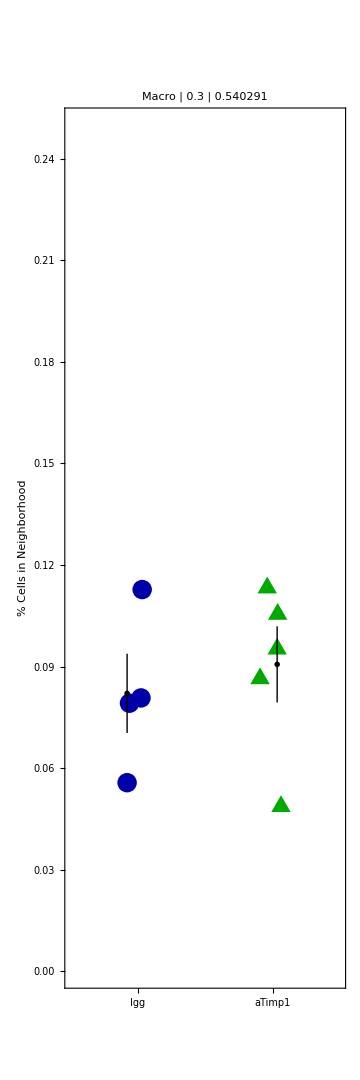
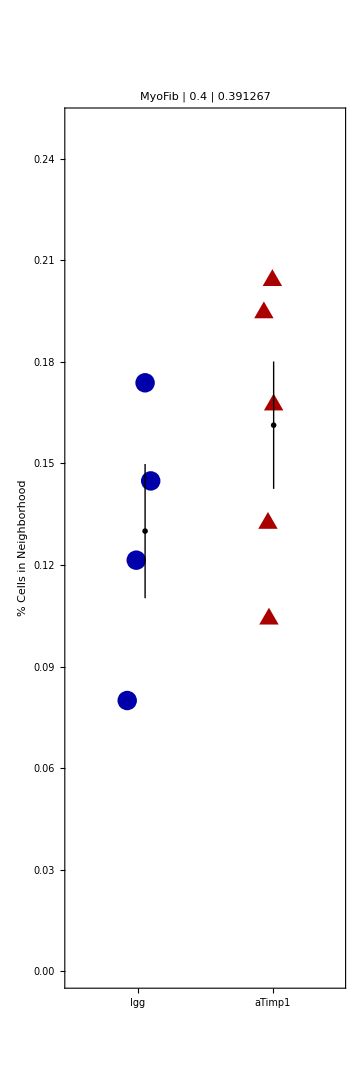

```mathematica
Row[

MapIndexed[

Show[{
ListPlot[
#,
AspectRatio->3,Frame->True,PlotRange->{{.5,2.5},{0,.25}},FrameTicks->{{Automatic,None},{{{1,"Igg"},{2,"aTimp1"}},None}},ImageSize->Medium,PlotMarkers->{{Graphics@Disk[],20},{Graphics@SSSTriangle[1,1,1],20}},PlotStyle->{Darker@Blue,Darker@{Green,Red}[[#2[[1]]]]},FrameLabel->{None,"% Cells in Neighborhood"},PlotLabel->(*{"M","myoF"}[[#2[[1]]]]*)TableForm[{{"Macro","MyoFib"}[[#2[[1]]]],{1,0}+MannWhitneyTest[#[[;;,;;,2]],Automatic,"TestData"]/{-1/2 Times@@(Length/@#),1}},TableAlignments->Center]],
ListPlot[{#[[1,1]],MeanAround[#[[;;,2]]]}&/@#,PlotStyle->Black,PlotMarkers->{"—",20}]}]&,
((Thread/@Thread[{{1,2},TakeList[Mean/@TakeList[#,{2,5,5,4,6,4,4,3,4}],{4,5}]}])/.x_Integer:>x+.1RandomReal[{-1,1}])&/@(((Join@@@counts[[;;,;;,2]])/.x:{_Integer..}:>N@((Total/@Partition[x,2][[{1,3}]])/(Total@x))/.x:{{_Real..}..}:>Mean[x])ᵀ)

],

Spacer@10]
```

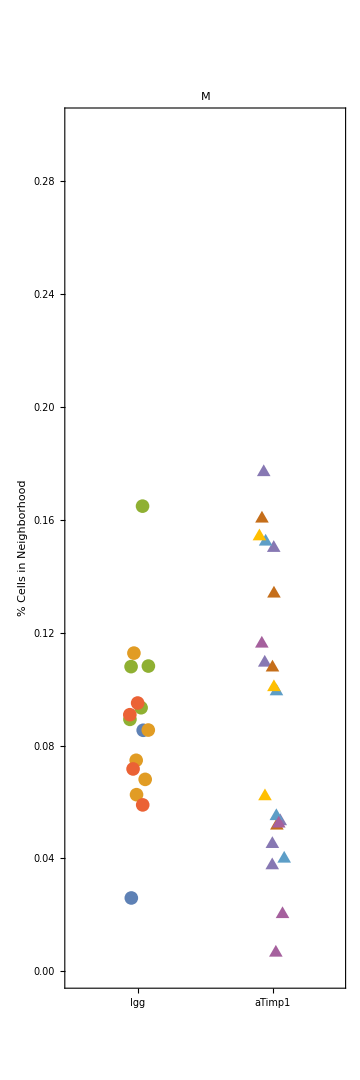
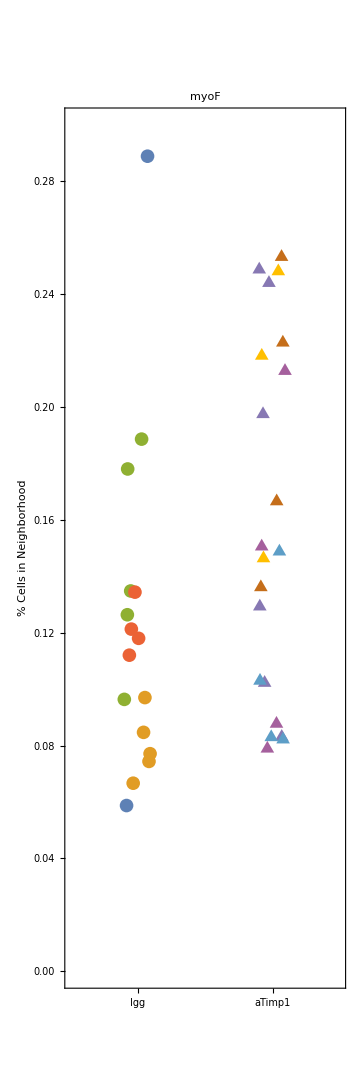

```mathematica
Row[
MapIndexed[ListPlot[
#/.x_Integer:>x+.1RandomReal[{-1,1}],
AspectRatio->3,Frame->True,PlotRange->{{.5,2.5},{0,.3}},FrameTicks->{{Automatic,None},{{{1,"Igg"},{2,"aTimp1"}},None}},ImageSize->Medium,PlotMarkers->Join[ConstantArray[{Graphics@Disk[],14},4],ConstantArray[{Graphics@SSSTriangle[1,1,1],14},5]],FrameLabel->{None,"% Cells in Neighborhood"},PlotLabel->{"M","myoF"}[[#2[[1]]]]]&,((Join@@Map[Thread,Thread/@({{1,2},#}ᵀ),{2}])&/@(TakeList[TakeList[#,{2,5,5,4,6,4,4,3,4}],{4,5}]&/@(((Join@@@counts[[;;,;;,2]])/.x:{_Integer..}:>N@((Total/@Partition[x,2][[{1,3}]])/(Total@x))/.x:{{_Real..}..}:>Mean[x])ᵀ)))],Spacer@10]
```

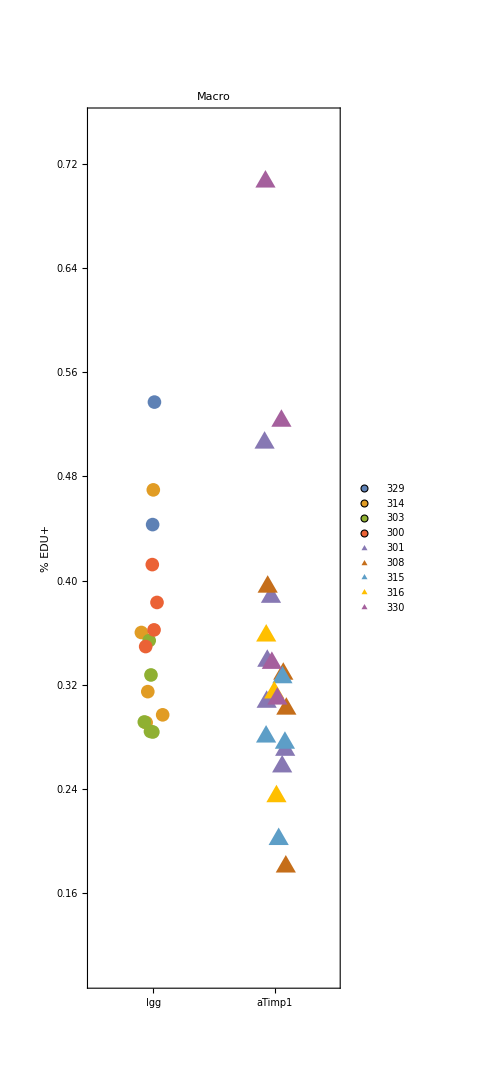
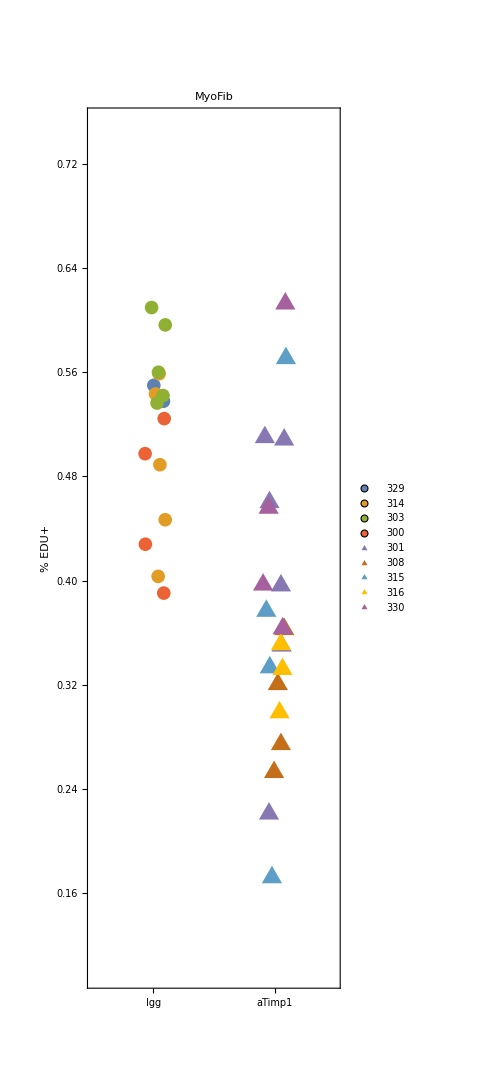

```mathematica
Row[
Table[
ListPlot[

Join@@Map[Thread,Thread/@({{1,2},Map[Mean@#&,DeleteCases[fractions[[;;,;;,;;,;;,i]],Indeterminate|0.,∞],{3}]}ᵀ),{2}]/.(x_Integer:>x+RandomReal[{-.1,.1}]),


AspectRatio->3,Frame->True,FrameTicks->{{Automatic,None},{{{1,"Igg"},{2,"aTimp1"}},None}},FrameLabel->{None,"% EDU+"},PlotRange->{{.5,2.5},{0.1,.75}},ImageSize->Medium,PlotStyle->PointSize[.05],PlotLegends->{"329","314","303","300","301","308","315","316","330"},PlotLabel->{"Macro","Other","MyoFib"}[[i]],PlotMarkers->Join[ConstantArray[{Graphics@Disk[],14},4],ConstantArray[{"▲",24},5]]],
{i,{1,3}}],
Spacer@20]
```

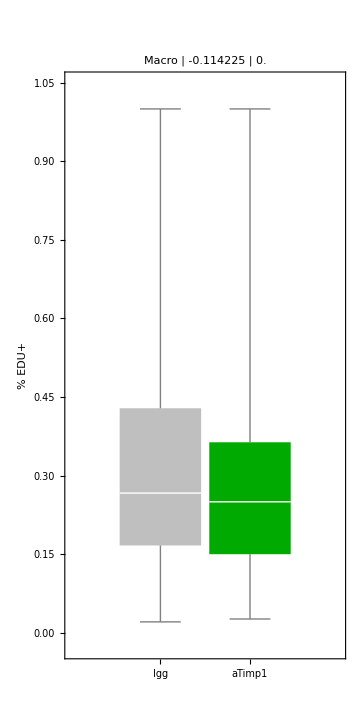
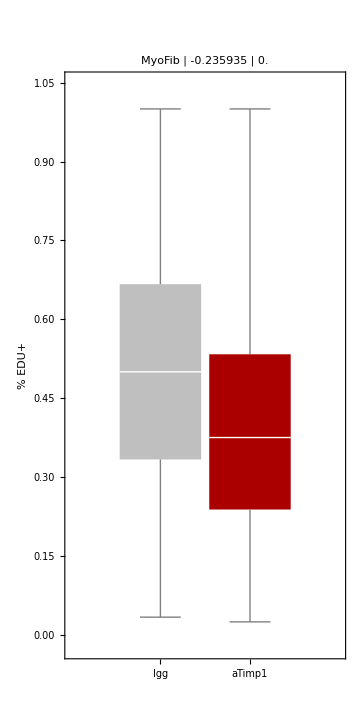

```mathematica
Row[Table[
BoxWhiskerChart[#,BarSpacing->{Tiny,Large},ImageSize->Medium,AspectRatio->2,ChartStyle->{GrayLevel[.75],{Darker@Green,Black,Darker@Red}[[i]]},PlotLabel->TableForm[{{"Macro","Other","MyoFib"}[[i]],{1,0}+MannWhitneyTest[#,Automatic,"TestData"]/{-1/2 Times@@(Length/@#),1}}],ChartLabels->{"Igg","aTimp1"},FrameLabel->{None,"% EDU+"}]&@DeleteCases[Join@@@Map[Join@@#&,fractions[[;;,;;,;;,;;,i]],{2}],Indeterminate|0.,∞],{i,{1,3}}],Spacer@10]
```

```mathematica
DeleteCases[fractions[[;;,;;,;;,3]],Indeterminate|0.,∞]
```

{{{{0.208333,1.},{0.0555556}},{{},{},{},{},{}},{{0.166667,0.09375,0.428571},{0.117647,0.5},{0.2,0.5},{0.333333,0.189189,0.727273},{0.2}},{{},{0.222222},{},{}}},{{{0.25,0.05},{},{0.2,0.375,0.2},{0.5,0.388889},{0.0833333,0.5},{}},{{0.25,0.25},{},{0.3},{}},{{0.0789474},{0.0454545},{0.0833333},{0.181818}},{{0.06,0.0769231},{0.214286,0.0666667,0.0909091},{0.0425532,0.538462}},{{0.666667,0.245614,0.5},{0.25,0.333333},{0.0666667,0.2},{0.0384615,0.454545}}}}

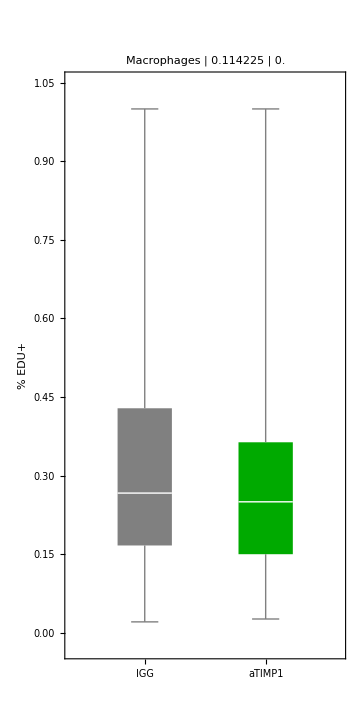
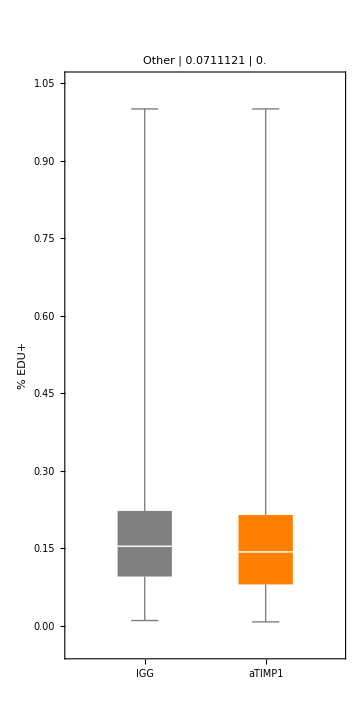
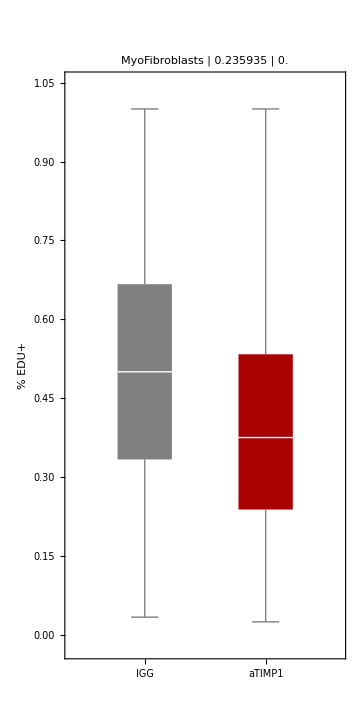

```mathematica
Row[Table[Quiet@BoxWhiskerChart[#,PlotLabel->TableForm[{{"Macrophages","Other","MyoFibroblasts"}[[p]],{1,0}+MannWhitneyTest[#,Automatic,"TestData"]/{-1/2 Times@@(Length/@#),1}}],ChartStyle->{Gray,{Darker@Green,Orange,Darker@Red}[[p]]},AspectRatio->2,ChartLabels->{"IGG","aTIMP1"},FrameLabel->{Automatic,"% EDU+"},ImageSize->Medium]&@DeleteCases[Flatten/@DeleteCases[fractions[[;;,;;,;;,;;,p]],Indeterminate,∞],0.,∞],
{p,{1,2,3}}],
Spacer@10]
```